```mathematica
richards[k_,r_,tm_,a_,t_]:=k/(1+Exp[-r(t-tm)])^(1/a);
```

```mathematica
fitModelToDataset[data_,model_,initialK_]:=NonlinearModelFit[data,model[k,r,tm,a,t],{{k,initialK},r,tm,a},t,MaxIterations->100000];
```

```mathematica
language="ObjectiveC";
```

```mathematica
percentage=100;
```

```mathematica
initialk=100000;
```

```mathematica
dataFilePath="/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes";
```

```mathematica
dataFileName=StringJoin["dados_",language,"_mes.dat"];
```

```mathematica
dataFull=Import[FileNameJoin[{dataFilePath,dataFileName}]];
```

```mathematica
exportPath=StringJoin[dataFilePath,"/processado_tail"];
```

```mathematica
mean[data_]:=Mean[data[[All,2]]];
```

```mathematica
ssRes[data_,model_]:=Sum[(data[[t,2]]-model[t])^2,{t,1,Length[data]}];
```

```mathematica
ssTot[data_]:=Sum[(data[[t,2]]-Mean[data[[All,2]]])^2,{t,1,Length[data]}];
```

```mathematica
rsquared[data_,model_]:=1-ssRes[data,model]/ssTot[data];
```

```mathematica
fittedFull=fitModelToDataset[dataFull,richards,initialk];
```

```mathematica
dataplotFull=ListPlot[dataFull[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"▲"}];
```

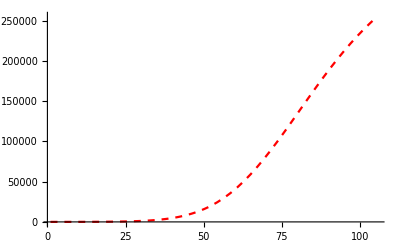

```mathematica
fitplotFull=Plot[fittedFull[t],{t,1,Length[dataFull]*1.1},PlotStyle->{Red,Dashed},PlotRange->All]
```

## 100%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*1]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,initialk];
```

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[100],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC100_fitParams.txt

## 90%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*0.9]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,1000000];
```

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[90],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC90_fitParams.txt

## 80%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*0.8]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,100000];
```

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[80],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC80_fitParams.txt

## 70%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*0.7]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,100000];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[70],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC70_fitParams.txt

## 60%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*0.6]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,50000];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[60],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC60_fitParams.txt

## 50%

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*0.5]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,100000];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;2]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{exportPath,StringJoin[language,ToString[50],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"]
```

/Users/emanoel/Dropbox/UFPE/Doutorado/Dados/github/ghtorrent/mathematica/programadores/mes/processado_tail/ObjectiveC50_fitParams.txt